```mathematica
ClearAll["Global`*"]
```

#### N = 2

```mathematica
n=2;
fixedPoints={{0,0.5},{1,0.5}};
points=Table[{Symbol["x"<>ToString@i],Symbol["y"<>ToString@i]},{i,1,n}];
$Assumptions=Flatten[Table[{Abs[Symbol["x"<>ToString@i]]>0,Abs[Symbol["y"<>ToString@i]]>0},{i,1,n}],1];
allPoints=Flatten[{points,fixedPoints},1]
allPointsNested=Table[{allPoints[[i]]},{i,1,allPoints//Length}];
colours=Flatten[{Table[Hue[i/n],{i,1,n}],{Black,Black}},1];
connections=Drop[Flatten[Table[allPoints[[i]]-allPoints[[j]],{i,1,allPoints//Length},{j,i+1,allPoints//Length}],1],-1]
```

{{x1,y1},{x2,y2},{0,0.5},{1,0.5}}

{{x1-x2,y1-y2},{x1,-0.5+y1},{-1+x1,-0.5+y1},{x2,-0.5+y2},{-1+x2,-0.5+y2}}

```mathematica
LPlot[ps_]:=ListPlot[allPointsNested/.ps[[2]],PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotStyle->colours,AspectRatio->1]
PlotLines[conns_,ps_]:=Graphics[Line[Table[{allPoints[[conns[[i,1]]]],allPoints[[conns[[i,2]]]]}/.ps[[2]],{i,1,conns//Length}]]]
PlotGraph[conns_,ps_]:=Show[LPlot[ps],PlotLines[conns,ps]]
```

```mathematica
attract[list_]:=Sum[Norm[allPoints[[list[[i,1]]]]-allPoints[[list[[i,2]]]]]^2,{i,1,list//Length}]
repulse[list_,K_]:=Sum[Norm[allPoints[[list[[i,1]]]]-allPoints[[list[[i,2]]]]]^-1*K^3,{i,1,list//Length}]
allRepulsions[K_]:=Sum[Norm[connections[[i]]]^-1*K^3,{i,1,connections//Length}]
averageConnection[]:=Sum[Norm[connections[[i]]],{i,1,connections//Length}]/(connections//Length)
```

{1.2678,{x1→0.5,x2→0.5,y1→0.394042,y2→0.605958}}

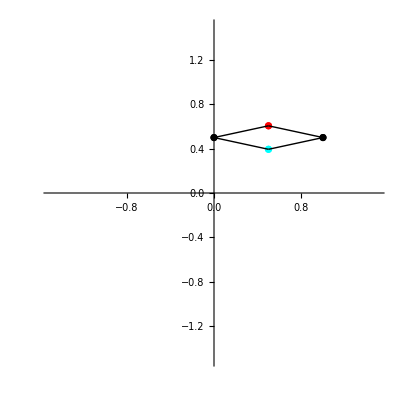

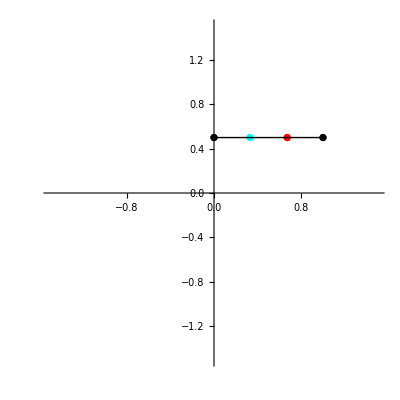

```mathematica
{{-2,1},{-2,2},{1,-1},{2,-1}};
attract[%]+allRepulsions[1]*1/(√n+1)^3/4;
NMinimize[%,{x1,x2,y1,y2}]
PlotGraph[%%%,%]
{{-2,1},{1,2},{2,-1}};
attract[%]+allRepulsions[1]*1/(√n+1)^3/4;
NMinimize[%,{x1,x2,y1,y2}];
PlotGraph[%%%,%]
```

#### N = 3

```mathematica
n=3;
fixedPoints={{0,0.5},{1,0.5}};
points=Table[{Symbol["x"<>ToString@i],Symbol["y"<>ToString@i]},{i,1,n}];
$Assumptions=Flatten[Table[{Abs[Symbol["x"<>ToString@i]]>0,Abs[Symbol["y"<>ToString@i]]>0},{i,1,n}],1];
allPoints=Flatten[{points,fixedPoints},1]
allPointsNested=Table[{allPoints[[i]]},{i,1,allPoints//Length}];
colours=Flatten[{Table[Hue[i/n],{i,1,n}],{Black,Black}},1];
connections=Drop[Flatten[Table[allPoints[[i]]-allPoints[[j]],{i,1,allPoints//Length},{j,i+1,allPoints//Length}],1],-1]
```

{{x1,y1},{x2,y2},{x3,y3},{0,0.5},{1,0.5}}

{{x1-x2,y1-y2},{x1-x3,y1-y3},{x1,-0.5+y1},{-1+x1,-0.5+y1},{x2-x3,y2-y3},{x2,-0.5+y2},{-1+x2,-0.5+y2},{x3,-0.5+y3},{-1+x3,-0.5+y3}}

```mathematica
LPlot[ps_]:=ListPlot[allPointsNested/.ps[[2]],PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotStyle->colours,AspectRatio->1]
```

```mathematica
attract[list_]:=Sum[Norm[allPoints[[list[[i,1]]]]-allPoints[[list[[i,2]]]]]^2,{i,1,list//Length}]
repulse[list_,K_]:=Sum[Norm[allPoints[[list[[i,1]]]]-allPoints[[list[[i,2]]]]]^-1*K^3,{i,1,list//Length}]
allRepulsions[K_]:=Sum[Norm[connections[[i]]]^-1*K^3,{i,1,connections//Length}]
```

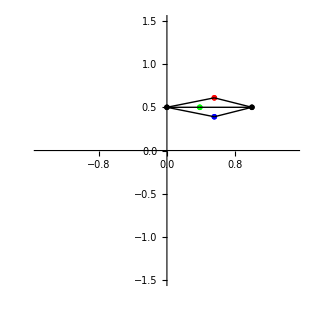

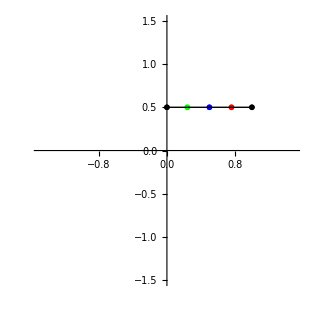

{{-2,1},{1,2},{2,3},{3,-1},{1,3}}

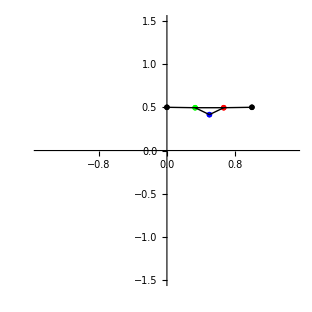

```mathematica
{{-2,1},{-2,2},{-2,3},{1,-1},{2,-1},{3,-1}};
attract[%]+allRepulsions[1]*1/(√n+1)^3/4;
NMinimize[%,{x1,x2,x3,y1,y2,y3}];
PlotGraph[%%%,%]
{{-2,1},{1,2},{2,3},{3,-1}};
attract[%]+allRepulsions[1]*1/(√n+1)^3/4;
NMinimize[%,{x1,x2,x3,y1,y2,y3}];
PlotGraph[%%%,%]
{{-2,1},{1,2},{2,3},{3,-1},{1,3}}
attract[%]+allRepulsions[1]*1/(√n+1)^3/4;
NMinimize[%,{x1,x2,x3,y1,y2,y3}];
PlotGraph[%%%,%]
```

#### N = 4

```mathematica
n=4;
fixedPoints={{0,0.5},{1,0.5}};
points=Table[{Symbol["x"<>ToString@i],Symbol["y"<>ToString@i]},{i,1,n}];
$Assumptions=Flatten[Table[{Abs[Symbol["x"<>ToString@i]]>0,Abs[Symbol["y"<>ToString@i]]>0},{i,1,n}],1];
allPoints=Flatten[{points,fixedPoints},1]
allPointsNested=Table[{allPoints[[i]]},{i,1,allPoints//Length}];
colours=Flatten[{Table[Hue[i/n],{i,1,n}],{Black,Black}},1];
connections=Drop[Flatten[Table[allPoints[[i]]-allPoints[[j]],{i,1,allPoints//Length},{j,i+1,allPoints//Length}],1],-1]
```

{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{0,0.5},{1,0.5}}

{{x1-x2,y1-y2},{x1-x3,y1-y3},{x1-x4,y1-y4},{x1,-0.5+y1},{-1+x1,-0.5+y1},{x2-x3,y2-y3},{x2-x4,y2-y4},{x2,-0.5+y2},{-1+x2,-0.5+y2},{x3-x4,y3-y4},{x3,-0.5+y3},{-1+x3,-0.5+y3},{x4,-0.5+y4},{-1+x4,-0.5+y4}}

```mathematica
LPlot[ps_]:=ListPlot[allPointsNested/.ps[[2]],PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotStyle->colours,AspectRatio->1]
```

```mathematica
attract[list_]:=Sum[Norm[allPoints[[list[[i,1]]]]-allPoints[[list[[i,2]]]]]^2,{i,1,list//Length}]
repulse[list_,K_]:=Sum[Norm[allPoints[[list[[i,1]]]]-allPoints[[list[[i,2]]]]]^-1*K^3,{i,1,list//Length}]
allRepulsions[K_]:=Sum[Norm[connections[[i]]]^-1*K^3,{i,1,connections//Length}]
```

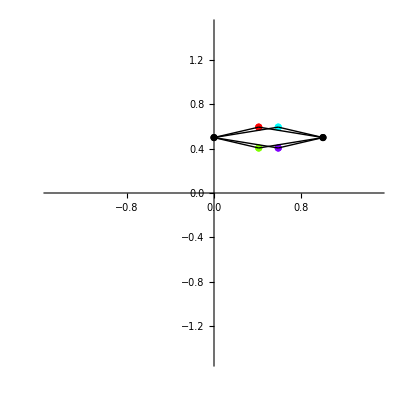

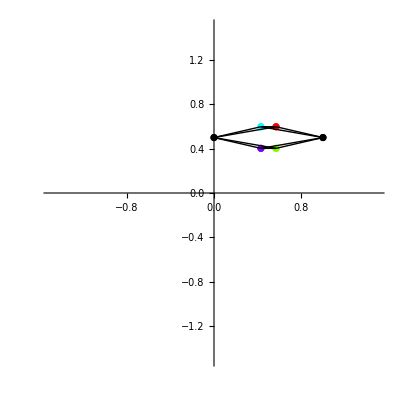

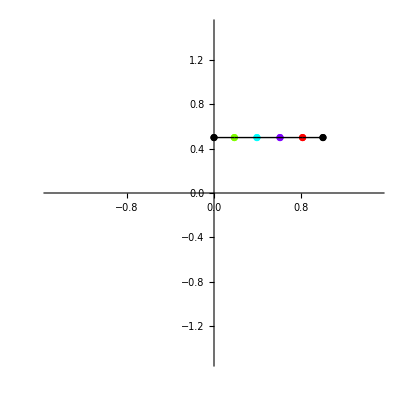

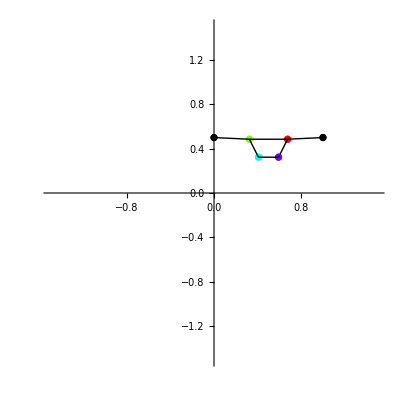

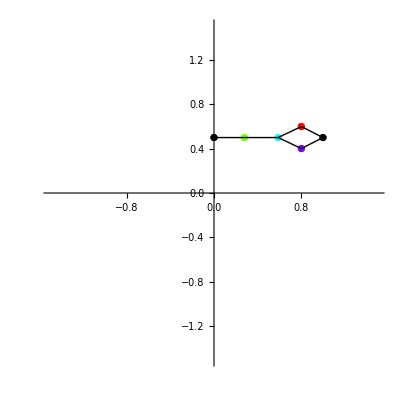

```mathematica
{{-2,1},{-2,2},{-2,3},{-2,4},{1,-1},{2,-1},{3,-1},{4,-1}};
attract[%]+allRepulsions[1]*1/(√n+1)^3/4;
NMinimize[%,{x1,x2,x3,x4,y1,y2,y3,y4}];
PlotGraph[%%%,%]
{{-2,1},{-2,2},{-2,3},{-2,4},{1,-1},{2,-1},{3,-1},{4,-1},{1,3},{2,4}};
attract[%]+allRepulsions[1]*1/(√n+1)^3/4;
NMinimize[%,{x1,x2,x3,x4,y1,y2,y3,y4}];
PlotGraph[%%%,%]
{{-2,1},{1,2},{2,3},{3,4},{4,-1}};
attract[%]+allRepulsions[1]*1/(√n+1)^3/4;
NMinimize[%,{x1,x2,x3,x4,y1,y2,y3,y4}];
PlotGraph[%%%,%]
{{-2,1},{1,2},{2,3},{3,4},{4,-1},{1,4}};
attract[%]+allRepulsions[1]*1/(√n+1)^3/4;
NMinimize[%,{x1,x2,x3,x4,y1,y2,y3,y4}];
PlotGraph[%%%,%]
{{-2,1},{1,2},{2,3},{2,4},{3,-1},{4,-1}};
attract[%]+allRepulsions[1]*1/(√n+1)^3/4;
NMinimize[%,{x1,x2,x3,x4,y1,y2,y3,y4}];
PlotGraph[%%%,%]
```

#### N = 4 no fixed

```mathematica
n=4;
fixedPoints={};
points=Table[{Symbol["x"<>ToString@i],Symbol["y"<>ToString@i]},{i,1,n}];
$Assumptions=Flatten[Table[{Abs[Symbol["x"<>ToString@i]]>0,Abs[Symbol["y"<>ToString@i]]>0},{i,1,n}],1];
allPoints=Flatten[{points,fixedPoints},1]
allPointsNested=Table[{allPoints[[i]]},{i,1,allPoints//Length}];
colours=Flatten[{Table[Hue[i/n],{i,1,n}],{Black,Black}},1];
connections=Flatten[Table[allPoints[[i]]-allPoints[[j]],{i,1,allPoints//Length},{j,i+1,allPoints//Length}],1]
```

{{x1,y1},{x2,y2},{x3,y3},{x4,y4}}

{{x1-x2,y1-y2},{x1-x3,y1-y3},{x1-x4,y1-y4},{x2-x3,y2-y3},{x2-x4,y2-y4},{x3-x4,y3-y4}}

```mathematica
LPlot[ps_]:=ListPlot[allPointsNested/.ps[[2]],PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotStyle->colours,AspectRatio->1]
```

```mathematica
attract[list_,K_]:=Sum[Norm[allPoints[[list[[i,1]]]]-allPoints[[list[[i,2]]]]]^2/K,{i,1,list//Length}]
repulse[list_,K_]:=Sum[Norm[allPoints[[list[[i,1]]]]-allPoints[[list[[i,2]]]]]^-1*K^2,{i,1,list//Length}]
allRepulsions[p_]:=Sum[Norm[connections[[i]]]^-p,{i,1,connections//Length}]
```

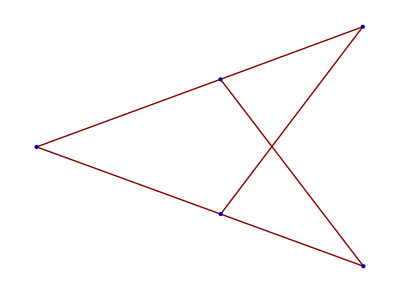

```mathematica
GraphPlot[{4->1,4->2,4->3,5->1,5->2,5->3},Method->"SpringElectricalEmbedding"]
```

{9.25007,{x1→-0.580197,x2→0.41537,x3→-0.453399,x4→0.288573,y1→0.564682,y2→-0.17729,y3→-0.304088,y4→0.69148}}

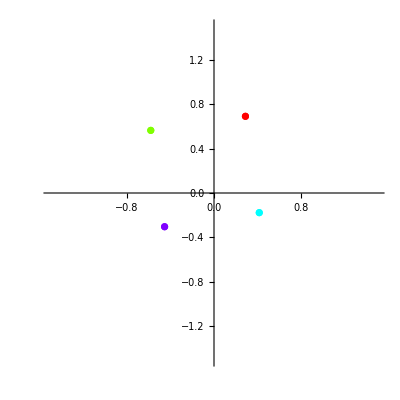

{7.23807,{x1→0.0174808,x2→0.58575,x3→-0.511573,x4→1.1148,y1→-0.480019,y2→-1.22816,y3→0.216492,y4→-1.92467}}

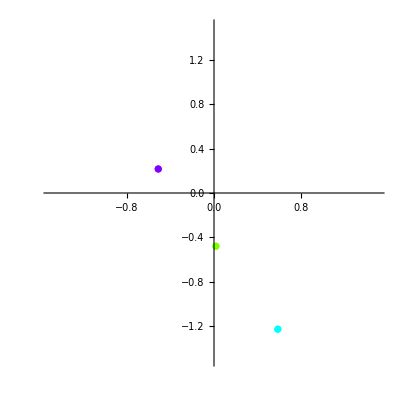

```mathematica
attract[{{3,1},{3,2},{1,4},{2,4}},1]+allRepulsions[1];
NMinimize[%,{x1,x2,x3,x4,y1,y2,y3,y4}]
LPlot[%]
attract[{{3,1},{1,2},{2,4}},1]+allRepulsions[1];
NMinimize[%,{x1,x2,x3,x4,y1,y2,y3,y4}]
LPlot[%]
```

#### N = 5 no fixed

```mathematica
n=5;
fixedPoints={};
points=Table[{Symbol["x"<>ToString@i],Symbol["y"<>ToString@i]},{i,1,n}];
$Assumptions=Flatten[Table[{Abs[Symbol["x"<>ToString@i]]>0,Abs[Symbol["y"<>ToString@i]]>0},{i,1,n}],1];
allPoints=Flatten[{points,fixedPoints},1]
allPointsNested=Table[{allPoints[[i]]},{i,1,allPoints//Length}];
colours=Flatten[{Table[Hue[i/(n-2)],{i,1,n-2}],{Black,Black}},1];
connections=Flatten[Table[allPoints[[i]]-allPoints[[j]],{i,1,allPoints//Length},{j,i+1,allPoints//Length}],1]
```

{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5}}

{{x1-x2,y1-y2},{x1-x3,y1-y3},{x1-x4,y1-y4},{x1-x5,y1-y5},{x2-x3,y2-y3},{x2-x4,y2-y4},{x2-x5,y2-y5},{x3-x4,y3-y4},{x3-x5,y3-y5},{x4-x5,y4-y5}}

```mathematica
LPlot[ps_]:=ListPlot[allPointsNested/.ps[[2]],PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotStyle->colours,AspectRatio->1]
```

```mathematica
attract[list_,K_]:=Sum[Norm[allPoints[[list[[i,1]]]]-allPoints[[list[[i,2]]]]]^2/K,{i,1,list//Length}]
repulse[list_,K_]:=Sum[Norm[allPoints[[list[[i,1]]]]-allPoints[[list[[i,2]]]]]^-1*K^2,{i,1,list//Length}]
allRepulsions[p_]:=Sum[Norm[connections[[i]]]^-p,{i,1,connections//Length}]
```

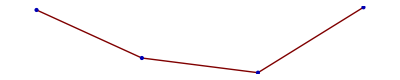

```mathematica
GraphPlot[{1->2,2->3,3->4},Method->"SpringElectricalEmbedding",]
```

{16.732,{x1→0.211314,x2→-0.342265,x3→0.251049,x4→-0.141934,x5→0.287118,y1→0.500817,y2→-0.220292,y3→-0.407406,y4→0.128603,y5→-0.0067077}}

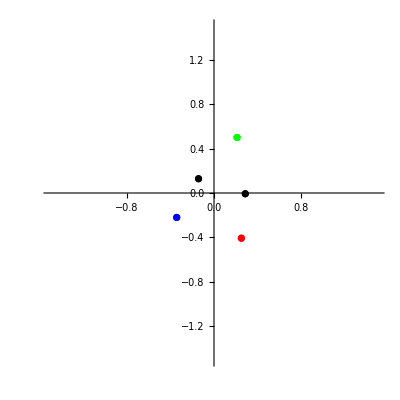

{10.3411,{x1→0.581817,x2→-0.381252,x3→-1.34432,x4→1.4591,x5→-2.2216,y1→0.682405,y2→0.562285,y3→0.442165,y4→0.791825,y5→0.332745}}

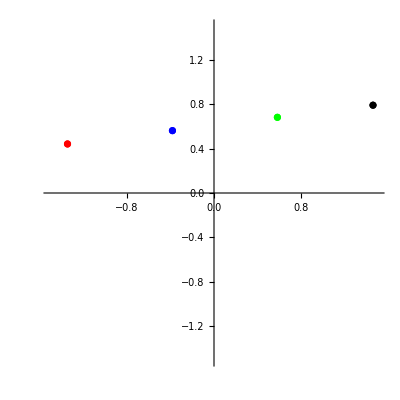

```mathematica
attract[{{4,1},{4,2},{1,5},{2,5},{4,3},{3,5}},0.51]+allRepulsions[0.51];
NMinimize[%,{x1,x2,x3,x4,x5,y1,y2,y3,y4,y5}]
LPlot[%]
attract[{{4,1},{1,2},{2,3},{3,5}},1]+allRepulsions[1];
NMinimize[%,{x1,x2,x3,x4,x5,y1,y2,y3,y4,y5}]
LPlot[%]
```

#### More

```mathematica
sumN2[p_]:=(Norm[V1O]^p+Norm[V2O]^p+Norm[VI1]^p+Norm[VI2]^p+Norm[V12]^p)/5;
sumN3[p_]:=(Norm[V1O]^p+Norm[V2O]^p+Norm[V3O]^p+Norm[VI1]^p+Norm[VI2]^p+Norm[VI3]^p+Norm[V12]^p+Norm[V13]^p+Norm[V23]^p)/9;
sum2[p_,p4_,n_:1,r_:1]:=n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p)+r*(Norm[V12]^-p4)
sum3[p_,p4_,n_:1,r_:1]:=n*(Norm[VI1]^p+Norm[V12]^p+Norm[V2O]^p)+r*(Norm[VI2]^-p4+Norm[V1O]^-p4)
sum4[p_,p4_,n_:1,r_:1]:=n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p+Norm[V3O]^p+Norm[VI3]^p)+r*(Norm[V12]^-p4+Norm[V13]^-p4+Norm[V23]^-p4)
sum5[p_,p4_,n_:1,r_:1]:=n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p)+r*(Norm[VI2]^-p4+Norm[V13]^-p4+Norm[V2O]^-p4)
sum6[p_,p2_,p3_,p4_,n_:1,t_:1,r_:1,g_:1]:=g*(Norm[VI1]^-p3+Norm[V2O]^-p3)/sumN3[1]^-p3+n*(Norm[VI1]^p+Norm[V12]^p+Norm[V23]^p+Norm[V3O]^p+Norm[V13]^p)+t*(Abs[Norm[VI1]-sumN3[1]]^p2+Abs[Norm[V12]-sumN3[1]]^p2+Abs[Norm[V23]-sumN3[1]]^p2+Abs[Norm[V3O]-sumN3[1]]^p2+Abs[Norm[V13]-sumN3[1]]^p2)+r*(Norm[VI2]^-p4+Norm[VI3]^-p4+Norm[V1O]^-p4+Norm[V2O]^-p4)/sumN3[1]^-p4
sum7[p_,p2_,p3_,p4_,n_:1,t_:1,r_:1,g_:1]:=g*(Norm[V1O]^-p3+Norm[VI1]^-p3+Norm[V2O]^-p3+Norm[VI2]^-p3+Norm[V3O]^-p3+Norm[VI3]^-p3)/sumN3[1]^-p3+n*(Norm[V1O]^p+Norm[VI1]^p+Norm[V2O]^p+Norm[VI2]^p+Norm[V3O]^p+Norm[VI3]^p+Norm[V13]^p)+t*(Abs[Norm[VI1]-sumN3[1]]^p2+Abs[Norm[VI2]-sumN3[1]]^p2+Abs[Norm[V1O]-sumN3[1]]^p2+Abs[Norm[V2O]-sumN3[1]]^p2+Abs[Norm[VI3]-sumN3[1]]^p2+Abs[Norm[V3O]-sumN3[1]]^p2+Abs[Norm[V13]-sumN3[1]]^p2)+r*(Norm[V12]^-p4+Norm[V23]^-p4)/sumN3[1]^-p4
```

{6.,{x1→-1.35105×10^-8,x2→-1.13695×10^-8,x3→-7.72126×10^-9,y1→-2.08104×10^-8,y2→-1.74042×10^-8,y3→-1.89778×10^-8}}

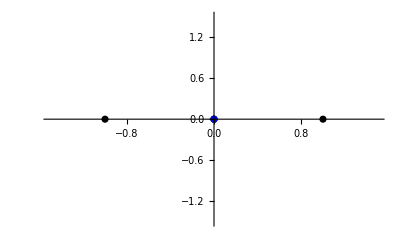

{6.,{x1→-0.979988,x2→-0.979988,x3→-0.979988,y1→5.88105×10^-8,y2→5.88104×10^-8,y3→5.88109×10^-8}}

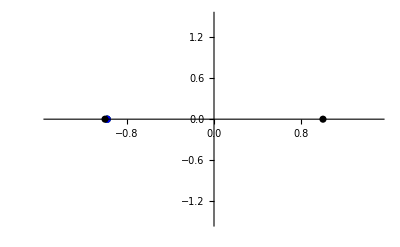

{5.69519,{x1→1.,x2→1.,x3→-1.,y1→-1.,y2→1.,y3→1.}}

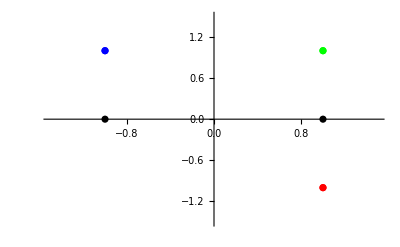

{4.05,{x1→1.,x2→1.06954×10^-7,x3→-1.,y1→1.,y2→-1.,y3→1.}}

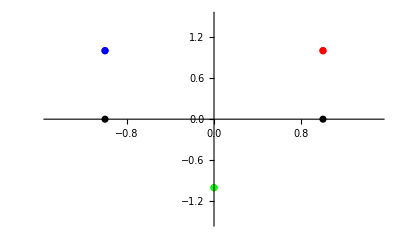

{18.4617,{x1→0.381781,x2→-1.61966×10^-8,x3→-0.381781,y1→0.623473,y2→-0.28849,y3→0.623473}}

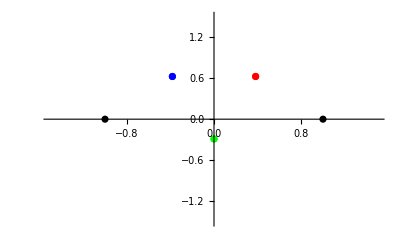

{18.8052,{x1→-0.174499,x2→-0.174499,x3→0.264646,y1→-0.410794,y2→0.410794,y3→-1.84056×10^-8}}

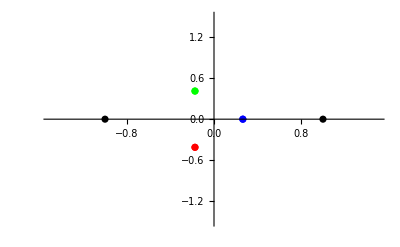

{17.7845,{x1→5.14201×10^-9,x2→0.505959,x3→-0.505959,y1→-0.337979,y2→0.947256,y3→0.947256}}

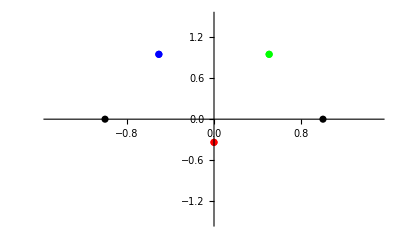

```mathematica
NMinimize[{sum[2],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[-1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[-2],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[-1]+sum[1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[-1]+sum[2],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum[-2]+sum[1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
```

```mathematica
sum4[2,1,1,1]/.{Abs[X_]->X};
%//Expand;
%/.{x1->0,x2->0,x3->0,y1->-0.86,y2->0.86,y3->0,n->1,t2->1}
```

94.0385

{5.88988,{x1→-0.137722,x2→0.137722,y1→0.372187,y2→-0.372187}}

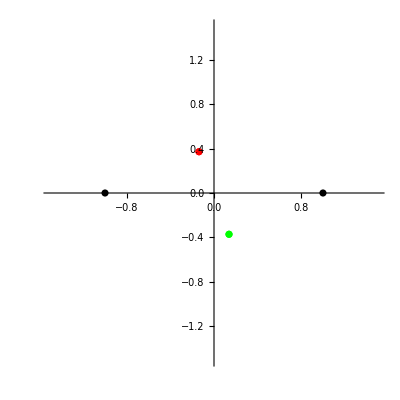

{2.78676,{x1→-0.416409,x2→0.416409,y1→-2.01615×10^-8,y2→-2.11512×10^-8}}

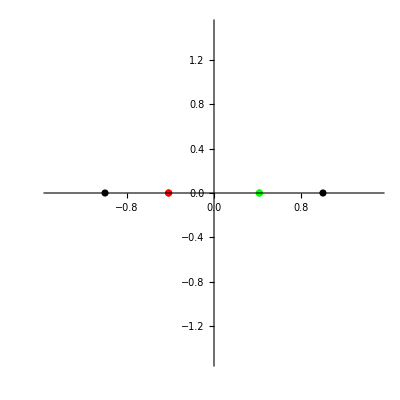

{10.9529,{x1→0.307464,x2→0.214331,x3→-0.521794,y1→-0.425002,y2→0.478772,y3→-0.0537703}}

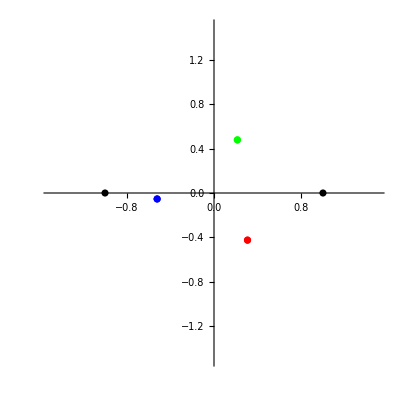

{3.85922,{x1→-0.648578,x2→-1.6047×10^-8,x3→0.648578,y1→-0.000958198,y2→-0.00191639,y3→-0.000958205}}

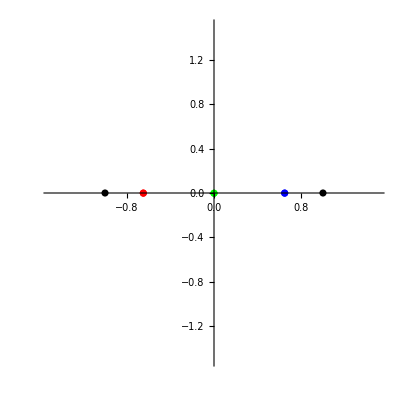

{4.90958,{x1→-0.291231,x2→-6.45039×10^-9,x3→0.291231,y1→1.44749×10^-8,y2→4.4581×10^-8,y3→1.43076×10^-8}}

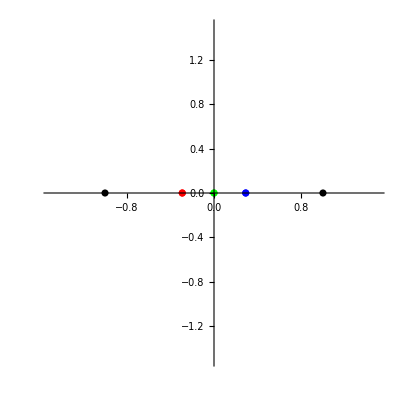

{9.89131,{x1→-0.111856,x2→1.82974×10^-8,x3→0.111856,y1→0.262087,y2→-0.497824,y3→0.262087}}

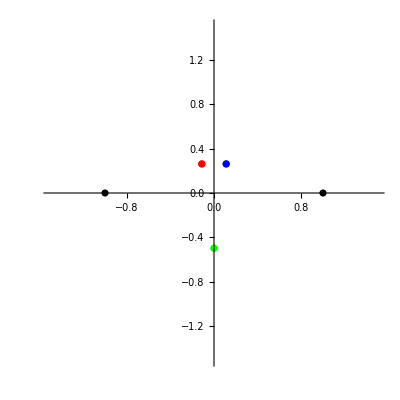

```mathematica
NMinimize[{sum2[2,1,1,1],Abs[x1]<=1,Abs[x2]<=1,Abs[y1]<=1,Abs[y2]<=1},{x1,x2,y1,y2}]
LPlot2[%]
NMinimize[{sum3[2,1,1,1],Abs[x1]<=1,Abs[x2]<=1,Abs[y1]<=1,Abs[y2]<=1},{x1,x2,y1,y2}]
LPlot2[%]
NMinimize[{sum4[2,1,1,1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum5[2,1,1,1],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum6[2,2,1,1,1,1,1,0],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
NMinimize[{sum7[2,2,1,1,1,1,1,0],Abs[x1]<=1,Abs[x2]<=1,Abs[x3]<=1,Abs[y1]<=1,Abs[y2]<=1,Abs[y3]<=1},{x1,x2,x3,y1,y2,y3}]
LPlot2[%]
```